# Split Drive Factorials

## 0) Functions

Plots

```mathematica
PlotLineDynamics[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/3
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
]
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

Data

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]

GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]

FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
ImportExperimentRawData[experimentString_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_*","AF1_*"};(*CHANGE TO AF1*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
ImportExperimentRawDataByNode[experimentString_,nodePattern_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch"<>nodePattern<>".csv","AF1_Aggregate_Patch"<>nodePattern<>".csv"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
CalculateGenotypesGroups[genotypes_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=StringPartition[#,1]&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
CalculateGenotypesGroupsOnLocus[genotypes_,locusRange_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=(StringPartition[#,1][[locusRange[[1]];;locusRange[[2]]]])&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
```

## 1) Load Data

```mathematica
SetDirectory["/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/"];
{experimentName,folderName}={"CRISPR","2018_11_27_ANALYZED"};
path=Directory[]<>"/"<>experimentName<>"/"<>folderName<>"/"
(**)
{startRelease,releasesInterval}={20,7};
{sweepIndices,anchor}={{2,3},6};
genotypesGroups={
{{2,5,5,6,7},"W"},
{{1,1,2,3,4},"H"},
{{3,6,8,8,9},"R"},
{{4,7,9,10,10},"B"},
{{4,7,9,10,10},"C"}
};
(*Define genotypes colors*)
originalColorsValues={
{0,90,50,0},
{90,50,0,0},
{50,100,0,0},
{0,100,0,0},
{0,100,0,25}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{rgbColors,genotypesGroups[[All,2]]}]//Grid;
(**)
folderPaths=FileNames["E_*",path];
folderNames=Last[StringSplit[#,"/"]]&/@folderPaths;
folderSplits=StringSplit[#,"_"]&/@folderNames;
Length[folderSplits]
```

/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/CRISPR/2018_11_27_ANALYZED/

500

## 2) Health Analysis

Single Run

/Volumes/Pusheen/xjego-khuq3/SplitDrive/Datasets/05/EqualHoming/CRISPR/2018_11_27_ANALYZED/E_03_01_080_080_25_10000

{ⅇ,3,1,80,80,25,10000}

194

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
WW | WH | WR | WB | HH | HR | HB | RR | RB | BB

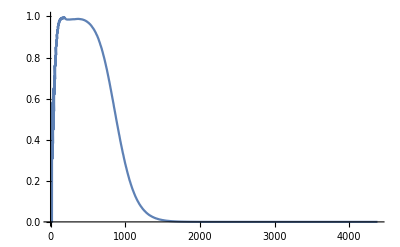

{1,80,25,522}

```mathematica
(**)
{patchString,threshold}={"0000",.8};
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"Hx"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};
genotypesGroups={
{{2,5,6,7},"Hx"},
{{1,3,4,8,9,10},"Other"}
};
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[5]]
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
(*Releases*)
releasesEnd=startRelease+(releasesNum*releasesInterval)-1
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[1]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
ListLinePlot[ratios,PlotRange->{0,1}]

suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,suppressionTime}
```

MultiRun

```mathematica
factorials=Table[
(**)
{patchString,threshold}={"0000",.8};
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"Hx"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};
genotypesGroups={
{{2,5,6,7},"Hx"},
{{1,3,4,8,9,10},"Other"}
};
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[i]];
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
(*Releases*)
releasesEnd=startRelease+(releasesNum*releasesInterval)-1;
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[1]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,If[suppressionTime>0,suppressionTime,0]}
,{i,1,Length[folderPaths]}];
Export[experimentName<>"_factorials.csv",factorials]
```

CRISPR_factorials.csv

```mathematica
factorials=Import[experimentName<>"_factorials.csv"];
anchors=factorials[[All,3]]//DeleteDuplicates;
Table[
filtered=Cases[factorials,{a_,b_,i,c_}->{a,b,c}];
plot=ListDensityPlot[filtered
,ColorFunction->ColorData[{"DeepSeaColors",{0,factorials[[All,4]]//Max}}]
,ColorFunctionScaling->False
,FrameLabel->(Style[#,20]&/@{"gRNA Fitness","Homing"})
,FrameStyle->Thick
,GridLines->{Range[-1.5,11,1],Range[75,101,2]}
,GridLinesStyle->Directive[Thick,Opacity[.75],LightGray]
,ImagePadding->Automatic
,InterpolationOrder->0
,PlotRange->{{-.5,10.5},{75,101},All}
,PlotRangePadding->None
,PlotRangeClipping->False
];
Export[experimentName<>StringPadLeft[ToString[i],3,"0"]<>".pdf",plot,ImageSize->750]
,{i,anchors}]
bl=BarLegend[{"DeepSeaColors",{0,factorials[[All,4]]//Max}},50];
Export[experimentName<>"bar"<>".png",bl,ImageSize->750,ImageResolution->250]
```

{CRISPR001.pdf,CRISPR005.pdf,CRISPR010.pdf,CRISPR020.pdf,CRISPR025.pdf}

CRISPRbar.png